#### Plot for gas flight times

```mathematica
flightTimeSound={795753,675551,585482,447364,336486};
flightTimeSoundError={ErrorBar@29927,ErrorBar@33533,ErrorBar@36235,ErrorBar@40379,ErrorBar@43705};

flightTimeTerminal={836854,767456,715454,635711,571696};
flightTimeTerminalError={ErrorBar@30776,ErrorBar@33659,ErrorBar@32336,ErrorBar@34729,ErrorBar@36649};

flightTimeMeasured={750000,650000,470000,4,5};
flightTimeMeasuredError={ErrorBar@25000,ErrorBar@25000,ErrorBar@25000,ErrorBar@25000,ErrorBar@25000};

amu={4,20,40,84,131};
```

```mathematica
Needs["ErrorBarPlots`"]
```

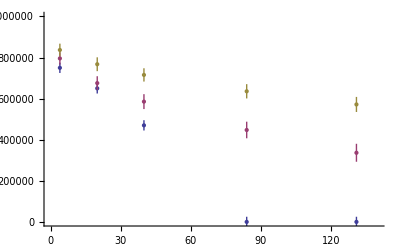

```mathematica
ErrorListPlot[{Transpose[{Transpose[{amu,flightTimeMeasured}],flightTimeMeasuredError}],Transpose[{Transpose[{amu,flightTimeSound}],flightTimeSoundError}],
Transpose[{Transpose[{amu,flightTimeTerminal}],flightTimeTerminalError}]},PlotRange->{{0,140},{0,10^6}}]
```